# Position projections

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## Spacing function

```mathematica
DTQWSpacing[rho_,"ForwardGrowing"]:=ArrayPad[rho,{{0,2},{0,2}}]
DTQWSpacing[rho_,"Growing"]:=ArrayPad[rho,2]
DTQWSpacing[rho_,"FixedSize"]:=rho
DTQWSpacing[rho_,s_String]:=With[{n=Read[StringToStream[StringDrop[s,-5]],Number]},
ArrayPad[rho,{{0,2*n},{0,2*n}}]
]/;(StringTake[s,-5]=="Ahead")
DTQWSpacing[rho_,"Both"]:=ArrayPad[rho,2]
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_]]:=With[{
bigrho=DTQWSpacing[rho,env["Type"]]
},
Chop[ApplyOperator[#,bigrho]]&[env["Unitary"][Length[bigrho]/2]]/;Not[env["Decoherent"]]
]
DTQWStep[rho_,DTQWEnv[env_]]:=Module[{
bigrho=DTQWSpacing[rho,env["Type"]],
state
},
state=ApplyOperator[#,bigrho]&[env["Unitary"][Length[bigrho]/2]];
Inner[Chop[#1*ApplyOperator[#2[Length[bigrho]/2],state]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]/;(env[[1]]["Type"]=="TwoAhead")
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]/;(env[[1]]["Type"]=="Two")
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]/;(env[[1]]["Type"]=="TwoAhead")
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]/;(env[[1]]["Type"]=="Two")
```

## DTQWQuanticity

```mathematica
DTQWQuanticity[coin_,range_]:=Module[{env,probs,sds,lm,nlm,p},
Table[
env=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{1-p,p},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
probs=DTQWPosDistribution/@DTQWTrace[coin,100,env];
sds=DTQWPosStandardev/@probs;
lm=LinearModelFit[sds,x,x];
nlm=NonlinearModelFit[sds,A*Sqrt[x],{A},x];
{p,lm["AdjustedRSquared"],nlm["AdjustedRSquared"]},
{p,range}
]
]
(* Función incompleta, falta añadir funcionalidad usando la función para modificar envs *)
```

## Misc. functions

```mathematica
ApplyOperator[operator_?MatrixQ,rho_]:=operator.rho.ConjugateTranspose[operator]
ApplyOperator[operator_Function,rho_]:=operator[rho]
```

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=NonlinearModelFit[stdev,A*x,{A},x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
](* Revisar función luego *)
```

```mathematica
DTQWSummary[coin_,n_,env_]:=Module[{steps,probs,sds,adjst},
steps=DTQWTrace[coin,n,env];
probs=DTQWPosDistribution/@steps;
sds=DTQWPosStandardev/@probs;
adjst=DTQWSdAdjustments[sds];
{
ListLinePlot[probs[[-1]],
PlotLabel->"DTQW",
PlotRange->All,
Mesh->All
],
ListPlot[sds,
PlotLabel->adjst["BestFit"],
PlotRange->All
]
}
]
DTQWSummary[coin_,env_]:=DTQWSummary[coin,100,env]
```

## DTQW Matrix Plot

```mathematica
DTQWMatrixPlot[c0_,n_,env_,h_]:=Module[{dmats},
dmats=MatrixPartialTrace[#,h,{Round[Length[#]/2],2}]&/@DTQWTrace[c0,n,env];
ArrayPlot[#,
PlotLegends->Automatic,
ColorFunction->(Blend[{White,Blend[{Purple,Black},0.3]},#]&),
Mesh->True,
MeshStyle->Black
]&/@Table[m,{m,Abs[dmats]}]
]
```

## DTQW Equation Print

```mathematica
DTQWEquationPrint[probs_,kraus_]:=With[{tex="\\mathcal{E}(\\rho) = "<>Fold[#1<>"+"<>#2&,MapThread[#1<>""<>#2[[1]]<>"U \\rho U^\\dagger "<>#2[[2]]&,{probs,Map[If[""==#,{"",""},{#,#<>"^\\dagger "}]&,kraus]}]]},
URLExecute["https://math.vercel.app/",{"bgcolor"->"auto","from"->"\\LARGE "<>ToString[tex]<>".svg"}]//Style[#,TextAlignment->Center]&
]
```

## External stuff

```mathematica
Get["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/QMB.wl"]
```

SetDelayed::write: Tag Charting`ScaledTicks in Charting`ScaledTicks[{TicksFunction,CustomTicks[opts:OptionsPattern[]]},sc_,Nice][_,_,_] is Protected.

MatrixPartialTrace::shdw: Symbol MatrixPartialTrace appears in multiple contexts {QMB`,Global`}; definitions in context QMB` may shadow or be shadowed by other definitions.

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

```mathematica
RandomQubitState[]
```

{0.629766,-0.0201608+0.776523 ⅈ}

## Examples

## Operadores

```mathematica
α=π/6.;
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
PositionprojOperator[n_]:=Function[rho,DiagonalMatrix@Diagonal[rho]]
FuzzyOperator[n_]:=RotateRight[IdentityMatrix[2*n,SparseArray],2]
PermutationOperators[s_]:=Function[n,RotateRight[IdentityMatrix[2*n,SparseArray],2*s]]
```

## Cálculos

### Probs 0

```mathematica
env1=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{1,0}],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

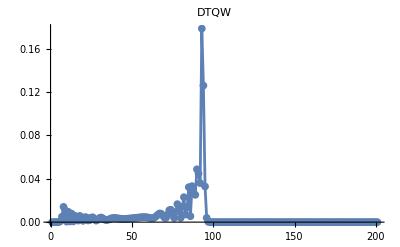
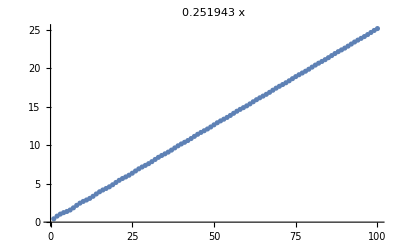

```mathematica
coinS0={1,0};
DTQWSummary[coinS0,100,env1]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf

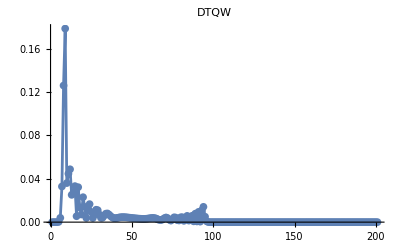
{-Graphics-,-Graphics-}

```mathematica
coinS1={0,1};
DTQWSummary[coinS1,100,env1]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf

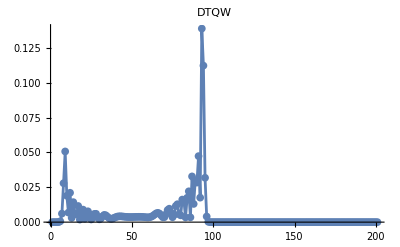
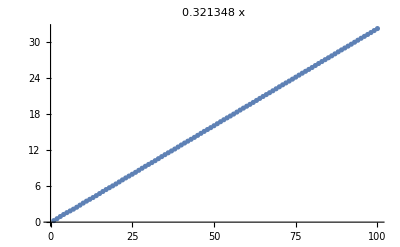

```mathematica
coinSpx={1,1}/Sqrt[2];
DTQWSummary[coinSpx,100,env1]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf

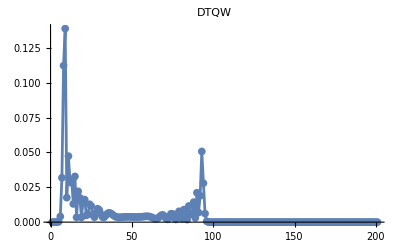
{-Graphics-,-Graphics-}

```mathematica
coinSmx={1,-1}/Sqrt[2];
DTQWSummary[coinSmx,100,env1]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf

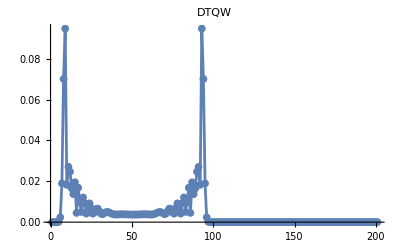
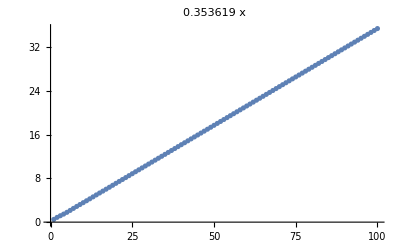

```mathematica
coinSpy={1,ⅈ}/Sqrt[2];
DTQWSummary[coinSpy,100,env1]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf

```mathematica
coinSmy={1,-ⅈ}/Sqrt[2];
DTQWSummary[coinSmy,100,env1]
```

{-Graphics-,-Graphics-}

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf

### Probs 0.01

```mathematica
env=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.99,0.01}],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

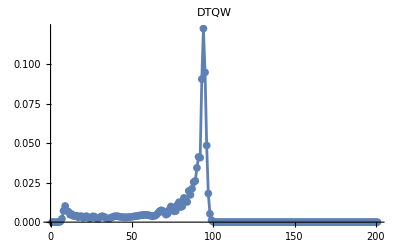
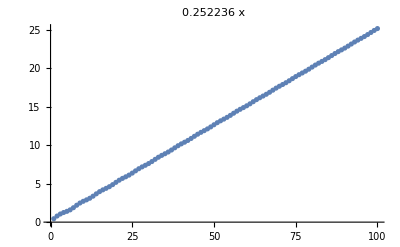

```mathematica
coinS0={1,0};
DTQWSummary[coinS0,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf

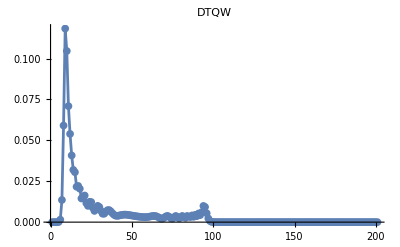
{-Graphics-,-Graphics-}

```mathematica
coinS1={0,1};
DTQWSummary[coinS1,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf

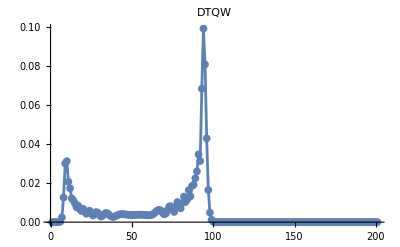
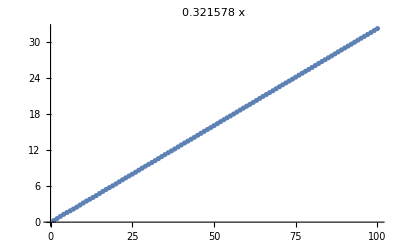

```mathematica
coinSpx={1,1}/Sqrt[2];
DTQWSummary[coinSpx,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf

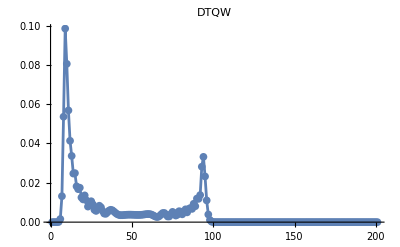
{-Graphics-,-Graphics-}

```mathematica
coinSmx={1,-1}/Sqrt[2];
DTQWSummary[coinSmx,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf

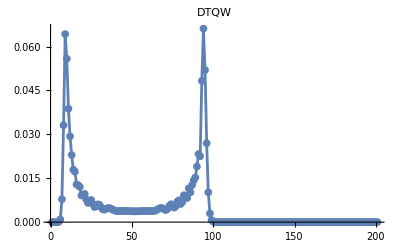
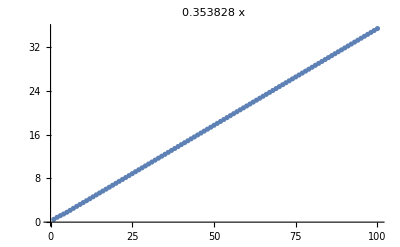

```mathematica
coinSpy={1,ⅈ}/Sqrt[2];
DTQWSummary[coinSpy,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf

```mathematica
coinSmy={1,-ⅈ}/Sqrt[2];
DTQWSummary[coinSmy,100,env]
```

{-Graphics-,-Graphics-}

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf

### Probs 0.1

```mathematica
env=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.9,0.1}],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

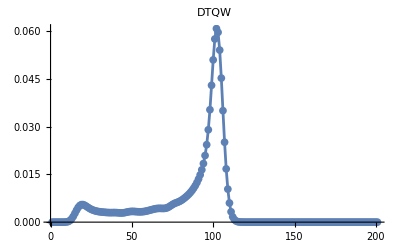
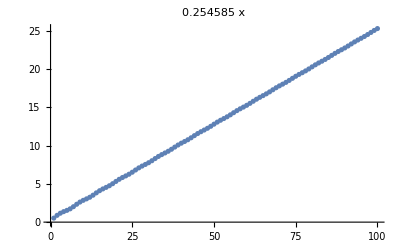

```mathematica
coinS0={1,0};
DTQWSummary[coinS0,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf

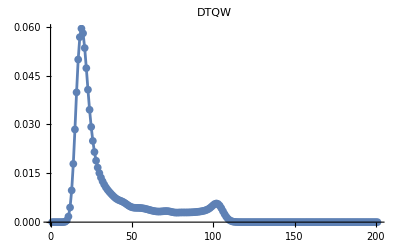
{-Graphics-,-Graphics-}

```mathematica
coinS1={0,1};
DTQWSummary[coinS1,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf

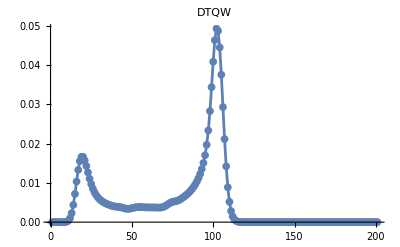
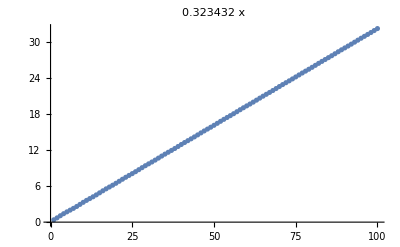

```mathematica
coinSpx={1,1}/Sqrt[2];
DTQWSummary[coinSpx,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf

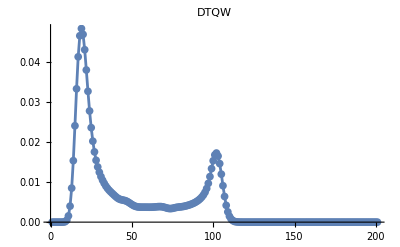
{-Graphics-,-Graphics-}

```mathematica
coinSmx={1,-1}/Sqrt[2];
DTQWSummary[coinSmx,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf

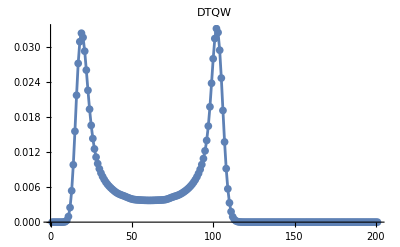
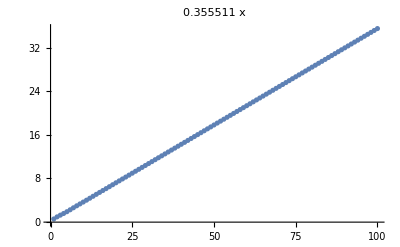

```mathematica
coinSpy={1,ⅈ}/Sqrt[2];
DTQWSummary[coinSpy,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf

```mathematica
coinSmy={1,-ⅈ}/Sqrt[2];
DTQWSummary[coinSmy,100,env]
```

{-Graphics-,-Graphics-}

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf

### Probs 0.25

```mathematica
env4=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.75,0.25}],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

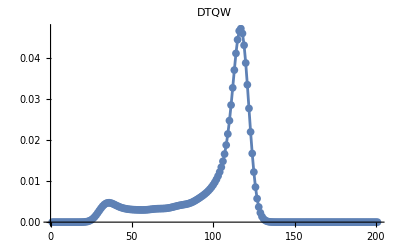
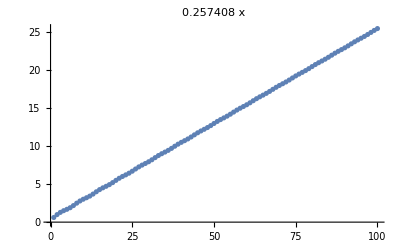

```mathematica
coinS0={1,0};
DTQWSummary[coinS0,100,env4]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf

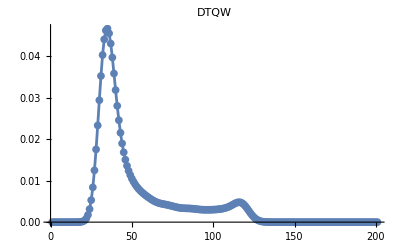
{-Graphics-,-Graphics-}

```mathematica
coinS1={0,1};
DTQWSummary[coinS1,100,env4]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf

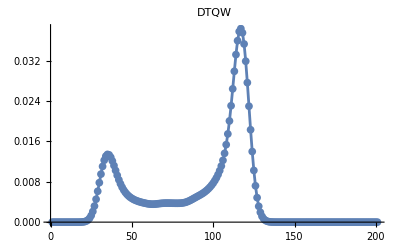
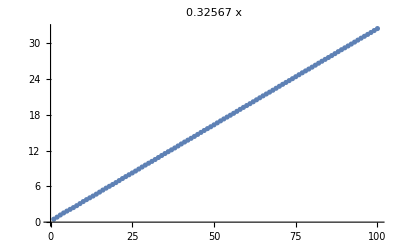

```mathematica
coinSpx={1,1}/Sqrt[2];
DTQWSummary[coinSpx,100,env4]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf

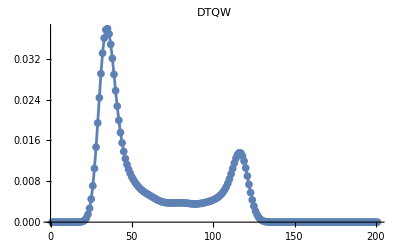
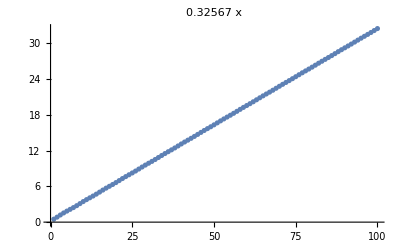

```mathematica
coinSmx={1,-1}/Sqrt[2];
DTQWSummary[coinSmx,100,env4]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf

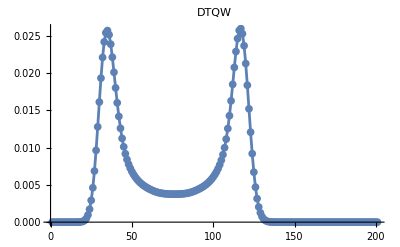
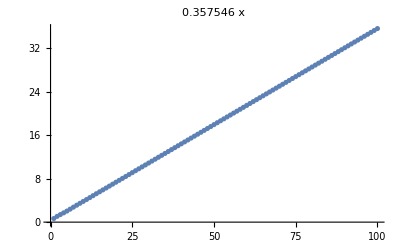

```mathematica
coinSpy={1,ⅈ}/Sqrt[2];
DTQWSummary[coinSpy,100,env4]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf

```mathematica
coinSmy={1,-ⅈ}/Sqrt[2];
DTQWSummary[coinSmy,100,env4]
```

{-Graphics-,-Graphics-}

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf

### Probs 0.5

```mathematica
env=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.5}~Join~ConstantArray[1/(2(#-1)),#-1]],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

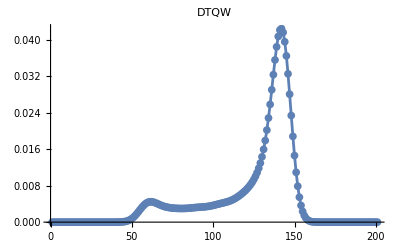
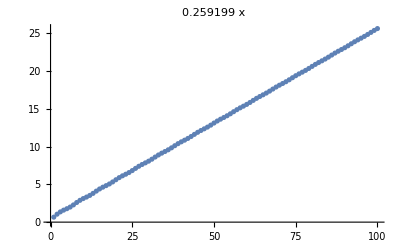

```mathematica
coinS0={1,0};
DTQWSummary[coinS0,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state0.pdf

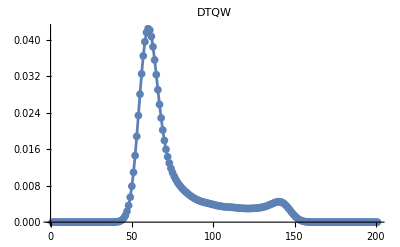
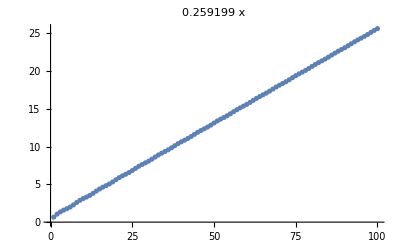

```mathematica
coinS1={0,1};
DTQWSummary[coinS1,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_state1.pdf

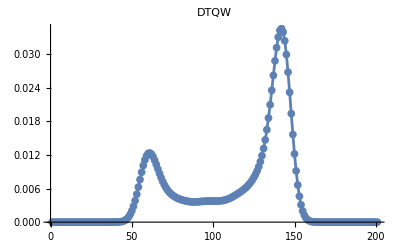
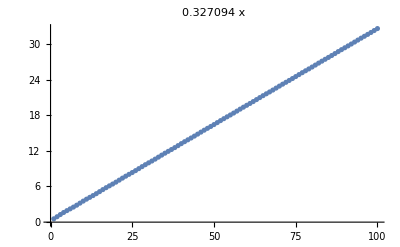

```mathematica
coinSpx={1,1}/Sqrt[2];
DTQWSummary[coinSpx,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepx.pdf

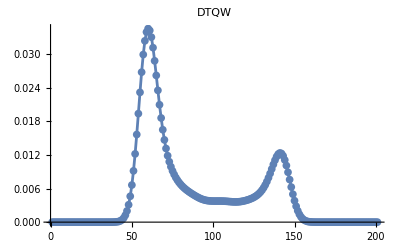
{-Graphics-,-Graphics-}

```mathematica
coinSmx={1,-1}/Sqrt[2];
DTQWSummary[coinSmx,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemx.pdf

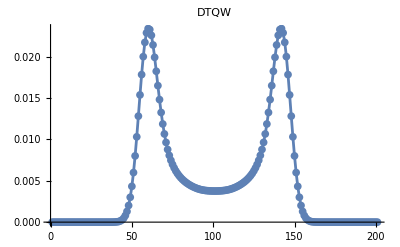
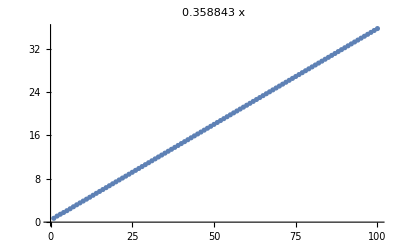

```mathematica
coinSpy={1,ⅈ}/Sqrt[2];
DTQWSummary[coinSpy,100,env]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statepy.pdf

```mathematica
coinSmy={1,-ⅈ}/Sqrt[2];
DTQWSummary[coinSmy,100,env]
```

{-Graphics-,-Graphics-}

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_statemy.pdf

## trasteando

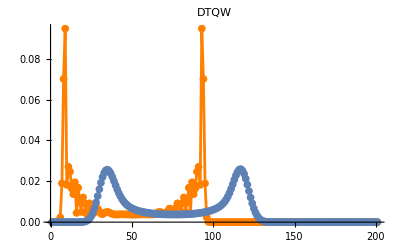

```mathematica
coinSmy={1,-ⅈ}/Sqrt[2];
Show[
a=DTQWSummary[coinSmy,100,env1][[1]]/.{RGBColor[_,_,_]->Orange},
DTQWSummary[coinSmy,100,env4][[1]]
]
```

```mathematica
env4=DTQWEnv[<|
"Type"->(ToString[#]<>"Ahead"),"Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->N[{0.75,0.25}],
"Kraus"->(PermutationOperators/@Range[0,#-1])
|>]&@2;
```

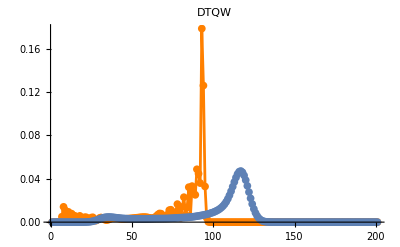

```mathematica
coin={1,0};
Show[
a=DTQWSummary[coin,100,env1][[1]]/.{RGBColor[_,_,_]->Orange},
DTQWSummary[coin,100,env4][[1]]
]
```

```mathematica
DTQWSummary[coin,100,env4][[1]]
```

-Graphics-

```mathematica
Module[{calc,mask,zeroes,ones,totals,positions},
calc=Partition[Diagonal@DTQW[coin,100,env4],2];
totals=Pick[#,(mask=Sign[#]),1]&@(Total/@calc);
positions=Pick[Range[Length[calc]],mask,1];
{zeroes,ones}=Pick[#,mask,1]&/@Transpose[calc];
{positions,Transpose[{zeroes/totals,ones/totals}]}
];
```

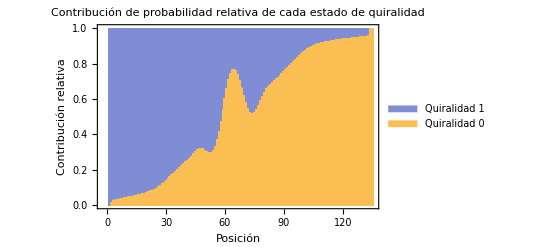

```mathematica
BarChart[#[[2]],
ChartLayout->"Stacked",
Frame->True,
Axes->False,
ChartLegends->{"Quiralidad 0","Quiralidad 1"},
PlotLabel->"Contribución de probabilidad relativa\nde cada estado de quiralidad",
FrameLabel->{"Posición","Contribución relativa"}
]&@%160
```

```mathematica
Table[If[Mod[i,7]==0,#[[1,i+1]],None],{i,0,Length[#[[1]]]-1}]&@%160
```

{12,None,None,None,None,None,None,19,None,None,None,None,None,None,26,None,None,None,None,None,None,33,None,None,None,None,None,None,40,None,None,None,None,None,None,47,None,None,None,None,None,None,54,None,None,None,None,None,None,61,None,None,None,None,None,None,68,None,None,None,None,None,None,75,None,None,None,None,None,None,82,None,None,None,None,None,None,89,None,None,None,None,None,None,96,None,None,None,None,None,None,103,None,None,None,None,None,None,110,None,None,None,None,None,None,117,None,None,None,None,None,None,124,None,None,None,None,None,None,131,None,None,None,None,None,None,138,None,None,None,None,None,None,145,None}

```mathematica
%160[[1]]
```

{12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146}

```mathematica
DTQWEquationPrint[{"p","q"},{"F_1","F_2"}]
```

-Graphics-